```mathematica
ClearAll["Global`*"]
```

```mathematica
<<"/Users/alexdeich/thesis/code/mine/ThesisTools.m"
```

About energy and angular momentum of particles- track t’[tau] and p’[tau] and recalculate Ee and Jz at each timestep, to get an ‘instantaneous’ conserved quantity?  no idea if this is valid.  For now, I’m just going to say that the newtonian contribution is a small perturbation and that the particle retains its angular momentum and energy.

```mathematica
SingleParticleNewtonianForce[InitVecs,mjze,2]
```

{-10000.,0.}

```mathematica
xy2radMotion[InitVecs[[2]],SingleParticleNewtonianForce[InitVecs,mjze,2]]
```

{{0.,0.0704888},{-10000.,0.}}

```mathematica
?xy2radMotion
```

xy2radMotion[{{x,y},{ẋ,ẏ}},{x^(..),y^(..)}] takes motion in Cartesian coördinates and returns motion in polar, {{ṙ,θ̇},({r)^(..),θ^(..)}}.

```mathematica
SingleParticleDerivativeVector[state_,consts_,i_,t_,M_,a_]:=Module[{f,Jz,Ee,r,rad,radmotion,rd,phi,G},
Ee = consts[[i,2]];
Jz = consts[[i,3]];
rad = xy2rad[{state[[i,1,1]],state[[i,1,2]]}];
r = rad[[1]];
phi = rad[[2]];
radmotion=xy2radMotion[state[[i]],SingleParticleNewtonianForce[state,consts,i]];
f={r,radmotion[[1,1]],phi,radmotion[[1,2]]};
G= {{f[[2]], (-3 (-a[t] Ee+Jz)^2 M+(-a[t]^2 (-4+Ee^2)+Jz^2) f[[1]]-4 M f[[1]]^2)/(4 f[[1]]^4)+radmotion[[2,1]]},{f[[4]],-(((a[t]^2 (a[t] Ee-Jz) M+f[[1]] (4 (-a[t]Ee+Jz) M^2+f[[1]] (3 a[t]Ee M-4 Jz M+Jz f[[1]]))) f[[2]])/(f[[1]]^2 (a[t]^2-2 M f[[1]]+f[[1]]^2)^2))+radmotion[[2,2]]}};
Return[G2xy[G,r,phi]];
]
```

State vector has {{{x,y},{xd,yd}},...}

```mathematica
a[x_]:=0;
InitVecs = {{{7.5,0},{0.,0.535715}},{{8,0},{0,0.535715}}};
mjze = {{1,5,7},{.0001,5,7}};
```

```mathematica
UpdateStateVectorsRK4[state_,consts_,tn_,dt_,M_,a_]:=Module[{Nparticles,NewState,i,k1state,k2state,k3state,k4state,k1,k2,k3,k4},
Nparticles = Length[state];
NewState = Table[{0},Nparticles];
For[i=1,i≤ Nparticles,i++,
k1state=state;
k2state=state;
k3state=state;
k4state=state;
k1=dt SingleParticleDerivativeVector[k1state,consts,i,tn+dt,M,a];
k2state[[i]] = state[[i]]+k1/2;
k2 = dt SingleParticleDerivativeVector[k2state,consts,i,tn+dt/2,M,a];
k3state[[i]]=state[[i]]+k2/2;
k3 = dt SingleParticleDerivativeVector[k3state,consts,i,tn+dt/2,M,a];
k4state[[i]] =state[[i]]+k3;
k4 = dt SingleParticleDerivativeVector[k4state,consts,i,tn+dt,M,a];
NewState[[i]] = state[[i]]+(1/3)(k1/2+k2+k3+k4/2);
];
Return[NewState];
]
```

```mathematica
TimeEvolveRK4[state_,consts_,t0_,dt_,timesteps_,M_,a_]:=Module[{wholestory,tn,n,NewVecs},
wholestory = Table[{0,0},timesteps];
tn =t0;
NewVecs = state;
wholestory[[1]] = {t0,state};
For[n=2,n≤ timesteps,n++,
NewVecs = UpdateStateVectorsRK4[NewVecs,consts,tn,dt,M,a];
tn=tn+dt;
wholestory[[n]]={tn,NewVecs};
];
Return[wholestory];
]
```

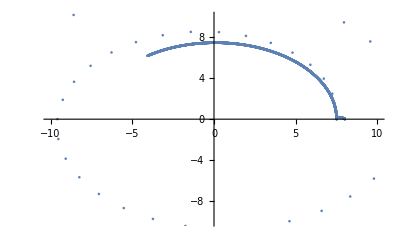

```mathematica
data = TimeEvolveRK4[InitVecs,mjze,0,0.01,nsteps,1,a];
pltrng=10;
xyplot1=ListPlot[Table[{data[[j,2,1,1,1]],data[[j,2,1,1,2]]},{j,1,nsteps}],PlotRange->{{-pltrng,pltrng},{-pltrng,pltrng}}];
xyplot2 = ListPlot[Table[{data[[j,2,2,1,1]],data[[j,2,2,1,2]]},{j,1,nsteps}],PlotRange->{{-pltrng,pltrng},{-pltrng,pltrng}}];
Show[{xyplot1,xyplot2}]
```

```mathematica
data[[1,2,2,1,1]]
```

-7.5

```mathematica
OneParticle = {{{7.5,0.},{0.,.535715}}};
```

```mathematica
mjze1 = {{1.,5.,7.}};
```

```mathematica
nsteps = 3000;
```

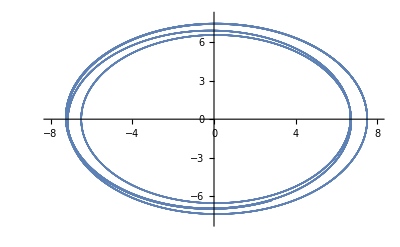

```mathematica
OneParticleData = TimeEvolveRK4[OneParticle,mjze1,0,0.01,nsteps,1,a];
xyplot=Table[{OneParticleData[[j,2,1,1,1]],OneParticleData[[j,2,1,1,2]]},{j,1,nsteps}];
pltrng=8;
ListPlot[{xyplot},PlotRange->{{-pltrng,pltrng},{-pltrng,pltrng}}]
```

```mathematica
T=0.;
r=7.5;
```

```mathematica
Td=0.0714286;
```

```mathematica
rd=0.
```

0.

```mathematica
xd = Cos[T] rd-r Sin[T] Td
```

0.

```mathematica
yd = Sin[T] rd+Cos[T] r Td
```

0.535715

```mathematica
r=Sqrt[x[t]^2+y[t]^2]
```

√(x[t]^2+y[t]^2)

```mathematica
FullSimplify[D[D[r,t],t]]
```

```mathematica
(y[t]^2 (x'[t]^2+x[t] x''[t])+x[t]^2 (y'[t]^2+x[t] x''[t])+y[t]^3 y''[t]+x[t] y[t] (-2 x'[t] y'[t]+x[t] y''[t]))/((x[t]^2+y[t]^2)^(3/2))
```

```mathematica
rdd[y_,yd_,ydd_,x_,xd_,xdd_]:=(y^2 (xd^2+x xdd)+x^2 (yd^2+x xdd)+y^3 ydd-x y (2 xd yd+x ydd))/((x^2+y^2)^(3/2))
```

```mathematica
rdd[0,.5357145,0,7.5,0,0]
```

0.0382653

To a certain extent, I don’t know why this works.  I edited xy2radMotion to output the “correct” velocity and acceleration vectors (that is, v={rd,r*td}, a={rdd-rtd^2,r*tdd+2rd*td}), but it didn’t give me the right result.  What did work was to use {rd,td} for velocity and the “correct” vector for acceleration.  Why does this work? Not sure:  maybe because you only use the velocity vector for the initial conditions, but the acceleration  is for the derivative vector? This suggests that if you were to time-evolve some system in polar coordinates, you would time-evolve the {rd,td} vector by the “correct” acceleration vector.  Ah ha! perhaps if you time evolve the {r,t} vector you would need the “correct” velocity vector as well.  perhaps.